```mathematica
Nlin[A_]=A*(A-1)/2//N;
Nip[A_]=A*(A-1)*(A-2)*(A-3)/8//N;
Nquad[A_]=Nlin[A]^2-Nlin[A]//N;
Sip[A_]=(Nlin[A]+Nip[A])/Nlin[A]//N;
Squad[A_]=(Nlin[A]+Nquad[A])/Nlin[A]//N;
```

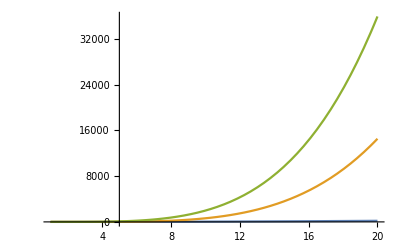

```mathematica
Plot[{Nlin[x],Nip[x],Nquad[x]},{x,1,20},PlotRange->All]
```

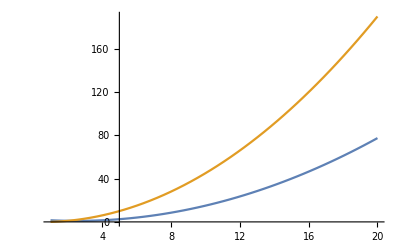

```mathematica
Plot[{Sip[x],Squad[x]},{x,1,20},PlotRange->All]
```

```mathematica
test={4,16,28};
Nlin[test]
Nip[test]
Nquad[test]
Sip[test]
Squad[test]
```

{6.,120.,378.}

{3.,5460.,61425.}

{30.,14280.,142506.}

{1.5,46.5,163.5}

{6.,120.,378.}